```mathematica
(* vacData *)
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm,ctex}"},"Magnification"->1.5];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["* Some Basic setup *"]
```

* Some Basic setup *

```mathematica
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
HideText["* Engine unchanged, possibly pdfLaTeX *"]
```

* Engine unchanged, possibly pdfLaTeX *

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
vacDataRAW=Import["data.xlsx"]⟦1⟧⟦All,#⟧&/@{{1,2},{4,5},{7,8},{10,11},{13,14},{16,17},{19,21}};
airDataRAW=Import["data.xlsx"]⟦2⟧⟦All,#⟧&/@{{1,2},{4,5},{7,9},{11,12}};
```

```mathematica
vacData=AssociationThread[Range[2,8],vacDataRAW];
airData=AssociationThread[{3,4,6,8},airDataRAW];
```

```mathematica
FindPeaks[#,16.4]&/@Values[vacData]⟦All,2;;,2⟧//N;
%//Column
vacPeaks=AssociationThread[Keys[vacData],Flatten[Select[50<#⟦1⟧<450&]/@%%,1]];
vacPeaks//Dataset
```

{{13.,3015.},{85.,2548.},{512.,2.}}
{{12.,2792.},{135.,2978.},{512.,6.}}
{{13.5,2282.},{185.,2923.},{512.,3.}}
{{13.,1865.},{227.,2646.},{512.,2.}}
{{13.,1267.},{285.,1769.},{512.,1.}}
{{15.,856.},{337.,932.},{512.,2.}}
{{13.,708.667},{386.,355.333}}

Dataset[<>]

```mathematica
sigma=16.4;
FindPeaks[#,sigma]&/@Values[vacData]⟦All,2;;,2⟧//N;
%//Column
vacPeaks=AssociationThread[Keys[vacData],Flatten[Select[50<#⟦1⟧<450&]/@%%,1]];
vacPeaks//Values//TableForm
```

{{13.,3015.},{85.,2548.},{512.,2.}}
{{12.,2792.},{135.,2978.},{512.,6.}}
{{13.5,2282.},{185.,2923.},{512.,3.}}
{{13.,1865.},{227.,2646.},{512.,2.}}
{{13.,1267.},{285.,1769.},{512.,1.}}
{{15.,856.},{337.,932.},{512.,2.}}
{{13.,708.667},{386.,355.333}}

85. | 2548.
135. | 2978.
185. | 2923.
227. | 2646.
285. | 1769.
337. | 932.
386. | 355.333

```mathematica
vacPeaks
```

<|2→{85.,2548.},3→{135.,2978.},4→{185.,2923.},5→{227.,2646.},6→{285.,1769.},7→{337.,932.},8→{386.,355.333}|>

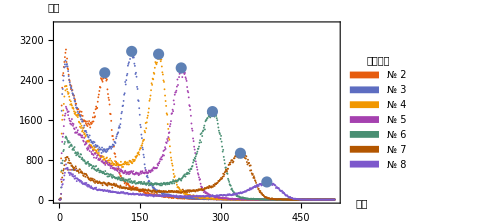

vacPlot.pdf

```mathematica
vacPlot=Show[ListPlot[Values[vacData],
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotRange->{0,3500},
PlotRangePadding->{{0,0},{0,Automatic}},
ImagePadding->{{50,40},{25,30}},
ImageSize->Medium,
GridLines->None,
PlotLegends->Placed[HoldForm@Evaluate@SwatchLegend[colors,
("№ "<>ToString[#])&/@Keys[vacData],
LegendMarkerSize->6,
LabelStyle->{FontSize->8,FontFamily->"Times New Roman"},
LegendLabel->Placed["出射窗口",{0,1}]],
{.85,.55}]],
ListPlot[vacPeaks//Values,
(*Callout[#1,#2,Above,
Appearance->"Line"]&@@@{{{300,2000},"huh\nhuh"}}*)
PlotMarkers->{omarker,.04}],
Epilog->(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{{"道址",Scaled[{1.075,0}]},{"计数",Scaled[{0,1.08}]}},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPlot
```

```mathematica
SystemOpen["vacPlot.pdf"]
```

```mathematica
vacColors=AssociationThread[Keys[vacData],Take[colors,Length[vacData]]];
```

```mathematica
Clear[slit]
```

```mathematica
vacPeaksShow[slit_,xrangeRel_,yrangeRel_,gridRel_]:=Module[{xrange,yrange,plot,grid},
xrange={vacPeaks[slit]⟦1⟧+xrangeRel⟦1⟧,vacPeaks[slit]⟦1⟧+xrangeRel⟦2⟧};
yrange={vacPeaks[slit]⟦2⟧+yrangeRel⟦1⟧,vacPeaks[slit]⟦2⟧+yrangeRel⟦2⟧};
grid={{vacPeaks[slit]⟦1⟧+gridRel⟦1,1⟧,vacPeaks[slit]⟦1⟧+gridRel⟦1,2⟧},
{vacPeaks[slit]⟦2⟧+gridRel⟦2,1⟧,vacPeaks[slit]⟦2⟧+gridRel⟦2,2⟧}};
plot=Show[ListPlot[{vacPeaks[slit]},
PlotTheme->"Scientific",
PlotStyle->GrayLevel[.8],
PlotMarkers->{omarker,.075},
PlotRange->{xrange,yrange},
GridLines->grid,
ImagePadding->{{40,40},{25,30}},
Epilog->(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{{"道址",Scaled[{1.075,0}]},{"计数",Scaled[{0,1.08}]}},
PlotLegends->Placed[HoldForm@Evaluate@SwatchLegend[
{vacColors[slit]},
("№ "<>ToString[#])&/@{slit},
LegendMarkerSize->6,
LabelStyle->{FontSize->10,
FontFamily->"Times New Roman"}],
Scaled[{.95,1}]],
PlotRangeClipping->False],
ListPlot[Select[Between[#⟦1⟧,xrange]
&&Between[#⟦2⟧,yrange]&]@vacData[slit],
PlotStyle->{vacColors[slit],PointSize[Medium]}]];
Return[Magnify[#,2]&@plot];
];
```

```mathematica
vacPeaks[2]
```

{85.,2548.}

```mathematica
vacPeak2=vacPeaksShow[2,{-sigma,sigma},{-500,150},{{-3,+3},{-100,50}}];
vacPeak3=vacPeaksShow[3,{-sigma,sigma},{-500,150},{{-3,+3},{-100,50}}];
vacPeak4=vacPeaksShow[4,{-sigma,sigma},{-500,150},{{-3,+3},{-100,50}}];
vacPeak5=vacPeaksShow[5,{-sigma,sigma},{-500,150},{{-3,+6},{-100,50}}];
vacPeak6=vacPeaksShow[6,{-sigma,sigma},{-500,150},{{-5,+5},{-100,50}}];
vacPeak7=vacPeaksShow[7,{-sigma,sigma},{-250,100},{{-5,+5},{-100,50}}];
vacPeak8=vacPeaksShow[8,{-2sigma,2sigma},{-250,100},{{-6,+6},{-100,50}}];
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak2;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak3;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak4;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak5;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak6;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak7;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@vacPeak8;
HideText["findPeaks"]
```

findPeaks

```mathematica
eFunction[n_]=-0.00437005655769313 (0.24046807248545032-n);
```

```mathematica
vacPeaksShift=AssociationThread[#1->#2]&@@Transpose@Import["data.xlsx"]⟦4⟧⟦2;;8,{1,11}⟧;
```

```mathematica
mod1Data=Import["data.xlsx"]⟦5⟧⟦2;;9,#⟧&@{1,2};
mod2Data=Import["data.xlsx"]⟦5⟧⟦2;;37,#⟧&@{4,5};
mod1=Interpolation[mod1Data,InterpolationOrder->1];
mod2=Interpolation[mod2Data,InterpolationOrder->1];
```

```mathematica
vacEPeaksWithError=Import["data.xlsx"]⟦4⟧⟦2;;8,{13,12}⟧;
((vacData⟦All,1,1⟧-6.15)/2*10^-2*60.3.4*10^-3*299792458/10^6)//Values;
vacPwithError={%,.1/(vacData⟦All,1,1⟧-6.15//Values)*%}ᵀ;
```

```mathematica
epPts=Join[vacPwithError⟦All,{1}⟧,vacEPeaksWithError⟦All,{1}⟧,2];
epError=ErrorBar@@@Join[vacPwithError⟦All,{2}⟧,vacEPeaksWithError⟦All,{2}⟧,2];
```

```mathematica
epRelations=Show[
Plot[{√((.511)^2+p^2)-.511,p^2/(2*.511)},{p,0,2.4},
PlotRange->{Automatic,{0,3}},
PlotTheme->"Scientific",
PlotStyle->Thickness[.002],
PlotRangePadding->{{0,0},{0,Automatic}},
ImagePadding->{{45,35},{40,32}},
ImageSize->Medium,
GridLines->None,
PlotLegends->Placed[HoldForm@Evaluate@LineLegend[colors,
{"相对论预测","经典预测"},
LegendMarkerSize->12,
LabelStyle->{FontSize->8,FontFamily->"Times New Roman"}],
{.25,.7}]],
ErrorListPlot[{epPts⟦#⟧,epError⟦#⟧}&/@Range[Length[epPts]],
PlotStyle->{GrayLevel[.35],PointSize[.001]},
ErrorBarFunction->Function[{coords, errs},
 {Opacity[1],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]
],
PlotRange->{{0,2.5},{0,3}},
Epilog->(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{
{MaTeX["p/\\frac{\\si{\\MeV}}{c}",Magnification->.8],Scaled[{.5,-.145}]},
{MaTeX["E/\\si{\\MeV}",Magnification->.8],Scaled[{0,1.08}]}},
PlotRangeClipping->False];
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@epRelations;
HideText["epRelations"]
```

epRelations

```mathematica
vacAirCompare[slit_]:=Module[{plot},
plot=Show[ListPlot[{vacData[slit]⟦2;;⟧,airData[slit]⟦2;;⟧},
PlotTheme->"Scientific",
PlotRange->{0,All},
PlotRangePadding->{{0,0},{0,300}},
ImagePadding->{{50,40},{25,30}},
ImageSize->Medium,
GridLines->None,
PlotLegends->Placed[HoldForm@Evaluate@SwatchLegend[colors⟦1;;2⟧,
(ToString[#])&/@{"真空情形","大气压下"},
LegendMarkerSize->8,
Spacings->.9,
LabelStyle->{FontSize->9,FontFamily->"黑体"}],
{.8,.75}]],
Epilog->Join[(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{
{"道址",Scaled[{1.075,0}]},
{"计数",Scaled[{0,1.08}]}},
{#}&@Inset[HoldForm@Evaluate@Style[
("№ "<>ToString[#])&@slit,
FontSize->10,
FontFamily->"Times New Roman"],
Scaled[{.95,1.08}]]],
PlotRangeClipping->False];
Return[(*Magnify[#,2]&@*)plot];
];
HideText["vacAirComp"]
```

vacAirComp

```mathematica
Export@@{StringDelete["Inactive"]@StringDelete["["]@StringDelete["]"]@ToString[#]<>".pdf",
Activate[#]}&/@Inactive[vacAirCompare]/@{3,4,6,8}
```

{vacAirCompare3.pdf,vacAirCompare4.pdf,vacAirCompare6.pdf,vacAirCompare8.pdf}

```mathematica
peaksN=AssociationThread[Range[2,8],Import["data.xlsx"]⟦4⟧⟦2;;8,7⟧];
```

```mathematica
plotBgRemoved[slit_,fitRange_]:=Show[vacAirCompare[slit],
Plot[Evaluate[a ⅇ^(-k n)/.Evaluate[(NonlinearModelFit[#,
{a ⅇ^(-k n)+b PDF[NormalDistribution[peaksN[slit],d],n]},
{a,b,d,k},n]["BestFitParameters"]&/@{
vacData[slit]⟦fitRange⟧,airData[slit]⟦fitRange⟧})]],
{n,1,512},
PlotTheme->"Scientific",
PlotStyle->Dashed]
];
plotBgRemoved3=plotBgRemoved[3,Join[Range[10,60],Range[250,513]]];
plotBgRemoved4=plotBgRemoved[4,Join[Range[10,60],Range[250,513]]];
plotBgRemoved6=plotBgRemoved[6,Join[Range[10,100],Range[350,513]]];
plotBgRemoved8=Show[plotBgRemoved[8,Join[Range[10,120],Range[350,513]]],
PlotRange->{{0,512},{0,350}}];
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotBgRemoved3;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotBgRemoved4;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotBgRemoved6;
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@plotBgRemoved8;
```

```mathematica
bgFunc[slit_,fitRange_]:=a ⅇ^(-k n)/.Evaluate[(NonlinearModelFit[#,
{a ⅇ^(-k n)+b PDF[NormalDistribution[peaksN[slit],d],n]},
{a,b,d,k},n]["BestFitParameters"]&/@{
vacData[slit]⟦fitRange⟧,airData[slit]⟦fitRange⟧})]
```

```mathematica
Table[bgFunc[3,Join[Range[10,60],Range[250,513]]]/.n->n0//N,{n0,2,10}]ᵀ
```

{{3235.04,3177.86,3121.69,3066.51,3012.31,2959.06,2906.76,2855.38,2804.91},{2307.02,2265.02,2223.79,2183.32,2143.57,2104.55,2066.25,2028.64,1991.71}}

```mathematica
(*bg3raw=(Table[bgFunc[3,Join[Range[10,60],Range[250,513]]]/.n->n0//N,{n0,2,513,1}]ᵀ);
bg4raw=(Table[bgFunc[4,Join[Range[10,60],Range[250,513]]]/.n->n0//N,{n0,2,513,1}]ᵀ);
bg6raw=(Table[bgFunc[6,Join[Range[10,100],Range[350,513]]]/.n->n0//N,{n0,2,513,1}]ᵀ);
bg8raw=(Table[bgFunc[8,Join[Range[10,120],Range[350,513]]]/.n->n0//N,{n0,2,513,1}]ᵀ);*)
```

```mathematica
(*Export["bg.dat",{bg3raw⟦1⟧,bg3raw⟦2⟧,
bg4raw⟦1⟧,bg4raw⟦2⟧,
bg6raw⟦1⟧,bg6raw⟦2⟧,
bg8raw⟦1⟧,bg8raw⟦2⟧}];*)
```

```mathematica
{bg3⟦1⟧,bg3⟦2⟧,
bg4⟦1⟧,bg4⟦2⟧,
bg6⟦1⟧,bg6⟦2⟧,
bg8⟦1⟧,bg8⟦2⟧}=Import["bg.dat"];
```

```mathematica
ListPlot[vacData[3]⟦2;;,2⟧-bg3⟦1⟧,PlotRange->All];
ListPlot[airData[3]⟦2;;,2⟧-bg3⟦2⟧,PlotRange->All];
vacPeak3Range=30;;200;
peak3vac=vacData[3]⟦vacPeak3Range,2⟧-bg3⟦1,vacPeak3Range⟧//Select[#>0&];
airPeak3Range=30;;260;
peak3air=airData[3]⟦airPeak3Range,2⟧-bg3⟦2,airPeak3Range⟧//Select[#>0&];
Row[{"3vac:",Round[Plus@@peak3vac]}]
Row[{"3air:",Round[Plus@@peak3air]}]
```

3vac:111308

3air:59190

```mathematica
ListPlot[vacData[4]⟦2;;,2⟧-bg4⟦1⟧,PlotRange->All];
ListPlot[airData[4]⟦2;;,2⟧-bg4⟦2⟧,PlotRange->All];
vacPeak4Range=50;;260;
peak4vac=(vacData[4]⟦vacPeak4Range,2⟧-bg4⟦1,vacPeak4Range⟧)//Select[#>0&];
airPeak4Range=50;;280;
peak4air=airData[4]⟦airPeak4Range,2⟧-bg4⟦2,airPeak4Range⟧//Select[#>0&];
Row[{"4vac:",Round[Plus@@peak4vac]}]
Row[{"4air:",Round[Plus@@peak4air]}]
```

4vac:131269

4air:65565

```mathematica
ListPlot[vacData[6]⟦2;;,2⟧-bg6⟦1⟧,PlotRange->All];
ListPlot[airData[6]⟦2;;,2⟧-bg6⟦2⟧,PlotRange->All];
vacPeak6Range=50;;350;
peak6vac=(vacData[6]⟦vacPeak6Range,2⟧-bg4⟦1,vacPeak6Range⟧)//Select[#>0&];
airPeak6Range=50;;380;
peak6air=airData[6]⟦airPeak6Range,2⟧-bg4⟦2,airPeak6Range⟧//Select[#>0&];
Row[{"6vac:",Round[Plus@@peak6vac]}]
Row[{"6air:",Round[Plus@@peak6air]}]
```

6vac:107650

6air:45078

```mathematica
{{Round[Plus@@peak3vac],Round[Plus@@peak3air]},
{Round[Plus@@peak4vac],Round[Plus@@peak4air]},
{Round[Plus@@peak6vac],Round[Plus@@peak6air]}}//TableForm
```

111308 | 59190
131269 | 65565
107650 | 45078

```mathematica
Round[((vacData⟦All,1,1⟧-6.15)/2)/@{3,4,6},.1]//TableForm
```

6.3
7.5
9.8